```mathematica
(* TWO JETS (Rob Fender 2023/24) *)

Clear["Global`*"]
SetDirectory["~/Dropbox/TwoJets"];

(* need to make a small list for each source, which is proper motion,
distance and hence apparent speed *)

(* ADD ANGLES? FOR SOURCES WHERE WE KNOW THE ANGLE WE CAN GET BETTER HANDLE ON LOWER LIMIT TO GAMMA *)

(* Colums [1] Name, [2] proper motion (mas/day), [3] distance (kpc), [4] apparent speed (c), [5] angle to line of sight (degrees), [6] beta, [7] gamma, [8] beta*gamma, [9] accretor type, [10] Fast/Slow, [11] Locked/Precessing, [12] Subscript[(a^*), refl], [13] Subscript[(a^*), cont], [14] Subscript[(a^*), QPO] *) 

(* BLACK HOLES *)

(* inclination angles from ISSI / Dave except where noted *)
u1543={"4U1543",187,5.0,0,10,0,0,0,"BH",">F","L",0.98,0.8,0};
(* inclination from Zhang et al. *)

gx339={"GX339-4",40,10,0,40,0,0,0,"BH",">F","L",0.95,0,0.27};

j1550={"XTEJ1550",65,4.4,0,70,0,0,0,"BH",">F","?",0.55,0.34,0.34};

j1803={"J1803",33,8,0,70,0,0,0,"BH",">F","?",0.991,0,0};

j1820f={"MAXIJJ1820(fast)",77,3.0,0,70,0,0,0,"BH",">F","?",0.988,0.14,0.8};
j1820s={"MAXIJJ1820(slow)",18,3.0,0,70,0,0,0,"BH","S","?",0.988,0.14,0.8};

j1348={"MAXIJ1348",110,2.2,0,35,0,0,0,"BH","F","L",0.78,0.41,0};

grs1915={"GRS1915",24,9.4,0,65,0,0,0,"BH",">F","L",0.98,0.95,0.71};

groj1655={"GROJ1655",54,3.2,0,85,0,0,0,"BH",">F","L?",0.98,0.7,0.29};

j1535={"MAXIJ1535",44,4.1,0,55,0,0,0,"BH","F","?",0.99,0,0};

h1743={"H1743",20,8.5,0,70,0,0,0,"BH","F","?",0.98,0,0.5};

j1848={"J1848",44,3.4,0,76,0,0,0,"BH?","F","?",0.97,0,0};
(* inclination from Bahramian et al. *)

j1752={"J1752",34,3.5,0,34,0,0,0,"BH","S","L?",0.92,0,0};

exo1846={"EXO1846",15,4.5,0,73,0,0,0,"BH","S","?",0.99,0,0};
(* inclination from Williams et al. *)

v404={"V404",25,2.4,0,40,0,0,0,"BH","S","P",0.92,0,0};
(* chosen inclination is from X-ray and radio, optical may be misaligned *)

x1908={"X1908",3,8,0,60,0,0,0,"BH","S","?",0.55,0,0};
(* huge range in the table, seems to originate with Rushton paper *)

(* UNKNOWN ACCRETOR *)

ss433s={"SS433",8,5.5,0,79,0,0,0,"?","S","P",0, 0, 0};

cygx3f={"Cyg X-3(fast)",18,7.4,0,10,0,0,0,"?","F","L?",0,0,0};
cygx3s={"Cyg X-3(slow)",10,7.4,0,90,0,0,0,"?","S","P",0,0,0};
(* could these angles be different ? *)


(* NEUTRON STARS *)


cirx1s={"Cir X-1",16,6.5,0,86,0,0,0,"NS","S","P",0,0,0};
scox1s={"Sco X-1",35,2.8,0,40,0,0,0,"NS","S","P",0,0,0};
cygx2={ "Cyg X-2",6,9,0,60,0,0,0,"NS","S","?",0,0,0};
(* from Spencer *)

(* Clunky but works: performs operation to convert proper motion and distance to apparent speed *)
{u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2}={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2} /. {aa_,bb_,cc_,dd_,ee_,ff_,gg_,hh_,ii_,jj_,kk_,ll_,mm_,nn_} -> {aa,bb,cc,((bb/173.0)*cc),ee,ff,gg,hh,ii,jj,kk,ll,mm,nn} ;

(* Now calculate intrinsic beta *)
{u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2}={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2} /. {aa_,bb_,cc_,dd_,ee_,ff_,gg_,hh_,ii_,jj_,kk_,ll_,mm_,nn_} -> {aa,bb,cc,dd,ee,Clip[(dd/(Sin[ee Degree] + dd Cos [ee Degree])),{0,0.90}],gg,hh,ii,jj,kk,ll,mm,nn} ;

(* Now calculate intrinsic gamma *)
{u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2}={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2} /. {aa_,bb_,cc_,dd_,ee_,ff_,gg_,hh_,ii_,jj_,kk_,ll_,mm_,nn_} -> {aa,bb,cc,dd,ee,ff,(1-ff^2)^(-1/2),hh,ii,jj,kk,ll,mm,nn} ;

(* .. and finally the product βγ *)
{u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2}={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2} /. {aa_,bb_,cc_,dd_,ee_,ff_,gg_,hh_,ii_,jj_,kk_,ll_,mm_,nn_} -> {aa,bb,cc,dd,ee,ff,gg,ff*gg,ii,jj,kk,ll,mm,nn} ;

(* I need to manually set the lower limits on gamma and beta for 4U1543 and Cir X-1 URF since they're higher than 0.95/3.2 *)

u1543[[6]]=0.982;
u1543[[7]]=5.3;
u1543[[8]]=5.2;

breal[bapp_, thetadeg_]:= bapp/(Sin [thetadeg Degree] + bapp Cos [thetadeg Degree])

lorentz[b_]:=(1-b^2)^(-1/2)

(* compilation of all the jets *)
alljets={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2};

titles1={"Name","Proper motion","Dist","Apparent speed", "Inclination", "β","γ","βγ","Accretor","Fast/","Dir.","(a^*)_refl", "(a^*)_cont", "(a^*)_QPO"};
titles2={" ","(mas d^-1)","(kpc)", "(c)","(deg)"," "," "," ","BH/NS/?","/Slow?","(L/P/?)"," "," "," "}; 

(* titles1={"Name","Proper motion","Dist","Apparent speed", "Inclination", "β","γ","βγ"};
titles2={" ","(mas d^-1)","(kpc)", "(c)","(deg)","(c) "," "," "}; *)

alljetst={titles1,titles2,u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2};

alljetsmeerkat={u1543,gx339,j1820f,j1348,grs1915,j1535,j1848};
alljetsnomeerkat={j1550,j1803,j1820s, groj1655,  h1743,  j1752, exo1846, v404, x1908, ss433s, cygx3f, cygx3s, cirx1s, scox1s, cygx2};

M1=MatrixForm[alljetst] ;
M2=NumberForm[M1,3]
(* This prints out the table below for checking purposes *)

(* all the jets with URFs removed *)
alljetsnourf={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908,  ss433s, cygx3f, cygx3s,  cirx1s, scox1s, cygx2};

(* all the black holes *)
bh={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, v404, x1908};

(* black holes with beta * gamma < 1.0 *)
slowbh={j1820s,j1752,exo1846,v404,x1908};

(* all the superluminal black holes *)
superluminalbh={u1543,gx339,j1550,j1803,j1820f,j1348,grs1915,groj1655,j1535};

(* our odd friends with no clue if BH or NS *)
unknourf={ss433s,cygx3f,cygx3s};

(* all the neutron stars *)
nsnourf={cygx2,cirx1s,scox1s};

(* precessing or not *)
prec={ss433s,cirx1s,scox1s,v404,cygx3s};

(* single ejection only*)
singlenourf={j1550,j1803,j1820f,j1820s,j1535,h1743,j1848,exo1846,x1908,cygx3f,cygx2};

(* multiple ejections in same direction *)
fixednourf={u1543,gx339,j1348,grs1915,groj1655,j1752};

(* no evidence for precession *)
nonprecnourf={u1543,gx339, j1550,j1803,j1820f,j1820s,j1348, grs1915, groj1655, j1535, h1743, j1848, j1752, exo1846, x1908,   cygx3f,   cygx2};

Print[" |BH = Black Hole, NS = Neutron Star, S = Slow, F = Fast, >F = Fast and unconstrained, L = Locked, P = Precessing, ? = Unknown, a^* reported BH spins |"]
Print[" ********************** SET UP DONE ********************** "];
```

(Name | Proper motion | Dist | Apparent speed | Inclination | β | γ | βγ | Accretor | Fast/ | Dir. | (a^*)_refl | (a^*)_cont | (a^*)_QPO
  | (mas d^-1) | (kpc) | (c) | (deg) |   |   |   | BH/NS/? | /Slow? | (L/P/?) |   |   |  
4U1543 | 187 | 5. | 5.4 | 10 | 0.982 | 5.3 | 5.2 | BH | >F | L | 0.98 | 0.8 | 0
GX339-4 | 40 | 10 | 2.31 | 40 | 0.9 | 2.29 | 2.06 | BH | >F | L | 0.95 | 0 | 0.27
XTEJ1550 | 65 | 4.4 | 1.65 | 70 | 0.9 | 2.29 | 2.06 | BH | >F | ? | 0.55 | 0.34 | 0.34
J1803 | 33 | 8 | 1.53 | 70 | 0.9 | 2.29 | 2.06 | BH | >F | ? | 0.991 | 0 | 0
MAXIJJ1820(fast) | 77 | 3. | 1.34 | 70 | 0.9 | 2.29 | 2.06 | BH | >F | ? | 0.988 | 0.14 | 0.8
MAXIJJ1820(slow) | 18 | 3. | 0.312 | 70 | 0.298 | 1.05 | 0.313 | BH | S | ? | 0.988 | 0.14 | 0.8
MAXIJ1348 | 110 | 2.2 | 1.4 | 35 | 0.814 | 1.72 | 1.4 | BH | F | L | 0.78 | 0.41 | 0
GRS1915 | 24 | 9.4 | 1.3 | 65 | 0.895 | 2.24 | 2. | BH | >F | L | 0.98 | 0.95 | 0.71
GROJ1655 | 54 | 3.2 | 0.999 | 85 | 0.9 | 2.29 | 2.06 | BH | >F | L? | 0.98 | 0.7 | 0.29
MAXIJ1535 | 44 | 4.1 | 1.04 | 55 | 0.736 | 1.48 | 1.09 | BH | F | ? | 0.99 | 0 | 0
H1743 | 20 | 8.5 | 0.983 | 70 | 0.77 | 1.57 | 1.21 | BH | F | ? | 0.98 | 0 | 0.5
J1848 | 44 | 3.4 | 0.865 | 76 | 0.733 | 1.47 | 1.08 | BH? | F | ? | 0.97 | 0 | 0
J1752 | 34 | 3.5 | 0.688 | 34 | 0.609 | 1.26 | 0.768 | BH | S | L? | 0.92 | 0 | 0
EXO1846 | 15 | 4.5 | 0.39 | 73 | 0.365 | 1.07 | 0.391 | BH | S | ? | 0.99 | 0 | 0
V404 | 25 | 2.4 | 0.347 | 40 | 0.382 | 1.08 | 0.413 | BH | S | P | 0.92 | 0 | 0
X1908 | 3 | 8 | 0.139 | 60 | 0.148 | 1.01 | 0.15 | BH | S | ? | 0.55 | 0 | 0
SS433 | 8 | 5.5 | 0.254 | 79 | 0.247 | 1.03 | 0.255 | ? | S | P | 0 | 0 | 0
Cyg X-3(fast) | 18 | 7.4 | 0.77 | 10 | 0.826 | 1.78 | 1.47 | ? | F | L? | 0 | 0 | 0
Cyg X-3(slow) | 10 | 7.4 | 0.428 | 90 | 0.428 | 1.11 | 0.473 | ? | S | P | 0 | 0 | 0
Cir X-1 | 16 | 6.5 | 0.601 | 86 | 0.578 | 1.23 | 0.709 | NS | S | P | 0 | 0 | 0
Sco X-1 | 35 | 2.8 | 0.566 | 40 | 0.526 | 1.18 | 0.619 | NS | S | P | 0 | 0 | 0
Cyg X-2 | 6 | 9 | 0.312 | 60 | 0.305 | 1.05 | 0.321 | NS | S | ? | 0 | 0 | 0)

|BH = Black Hole, NS = Neutron Star, S = Slow, F = Fast, >F = Fast and unconstrained, L = Locked, P = Precessing, ? = Unknown, a^* reported BH spins |

********************** SET UP DONE **********************

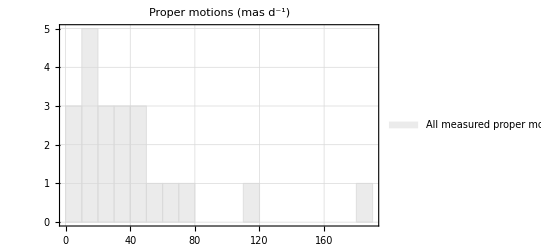

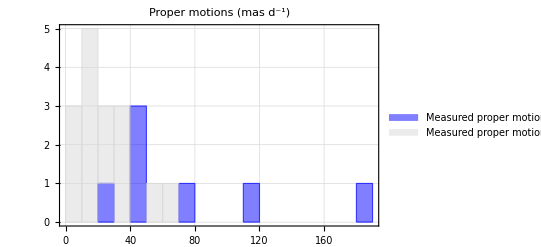

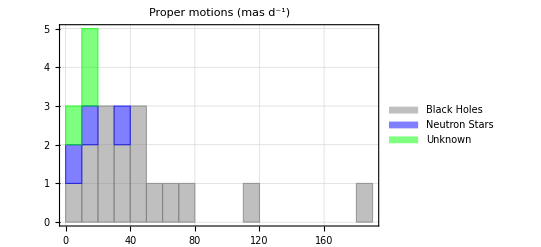

```mathematica
(* Plot the proper motions *)

pm=Histogram[{alljets[[All,2]]},{10},ChartStyle->{LightGray},PlotRange->Full,ChartLegends->Placed[{"All measured proper motions"},{0.6,0.8}],PlotLabel->"Proper motions (mas d^-1)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

pmkat=Histogram[{alljetsmeerkat[[All,2]],alljetsnomeerkat[[All,2]]},{10},ChartStyle->{Blue,LightGray},PlotRange->Full,ChartLegends->Placed[{"Measured proper motions (MeerKAT)","Measured proper motions (other)"},{0.6,0.8}],PlotLabel->"Proper motions (mas d^-1)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["pm.pdf",pm];
Export["pm.png",pm];

Export["pmkat.pdf",pmkat];
Export["pmkat.png",pmkat];

pmsep=Histogram[{bh[[All,2]],nsnourf[[All,2]],unknourf[[All,2]]},{10},ChartStyle->{Gray, Blue, Green},PlotRange->Full,ChartLegends->Placed[{"Black Holes","Neutron Stars","Unknown"},{0.8,0.8}],PlotLabel->"Proper motions (mas d^-1)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["pmsep.pdf",pmsep];
Export["pmsep.png",pmsep];

pmsepnourf=Histogram[{bh[[All,2]],nsnourf[[All,2]],unknourf[[All,2]]},{10},ChartStyle->{Gray, Blue, Green},PlotRange->Full,ChartLegends->Placed[{"Black Holes","Neutron Stars","Unknown"},{0.8,0.8}],PlotLabel->"Proper motions (mas d^-1), no URF",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

Export["pmsepnourf.pdf",pmsepnourf];
Export["pmsepnourf.png",pmsepnourf];
```

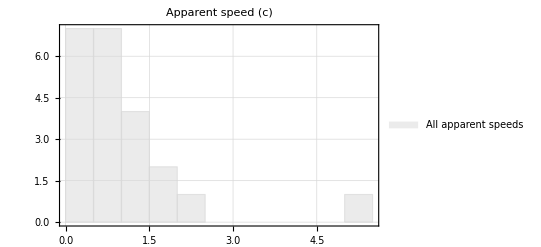

```mathematica
(* Plot the apparent speeds *)

speed=Histogram[{alljets[[All,4]]},{0.5},ChartStyle->{LightGray},PlotRange->Full,ChartLegends->Placed[{"All apparent speeds"},{0.6,0.8}],PlotLabel->"Apparent speed (c)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["speed.pdf",speed];
Export["speed.png",speed];
```

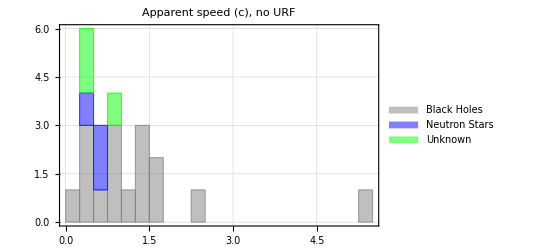

```mathematica
speedsepnourf=Histogram[{bh[[All,4]],nsnourf[[All,4]],unknourf[[All,4]]},{0.25},ChartStyle->{Gray, Blue, Green},PlotRange->Full,ChartLegends->Placed[{"Black Holes","Neutron Stars","Unknown"},{0.8,0.8}],PlotLabel->"Apparent speed (c), no URF",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["speedsepnourf.pdf",speedsepnourf];
Export["speedsepnourf.png",speedsepnourf];
```

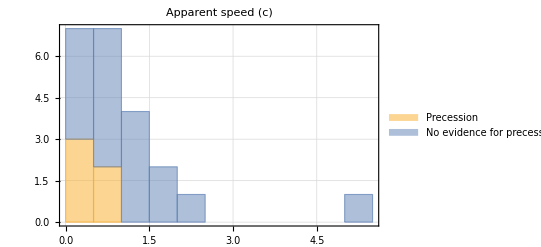

```mathematica
speedprec=Histogram[{prec[[All,4]],nonprecnourf[[All,4]]},{0.5},PlotRange->Full,ChartLegends->Placed[{"Precession","No evidence for precession"},{0.6,0.8}],PlotLabel->"Apparent speed (c)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["prec.pdf",speedprec];
Export["prec.png",speedprec];
```

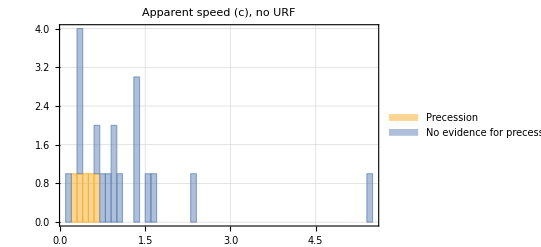

```mathematica
speedprecnourf=Histogram[{prec[[All,4]],nonprecnourf[[All,4]]},{0.1},PlotRange->Full,ChartLegends->Placed[{"Precession","No evidence for precession"},{0.6,0.8}],PlotLabel->"Apparent speed (c), no URF",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["precnourf.pdf",speedprecnourf];
Export["precnourf.png",speedprecnourf];
```

```mathematica
(* pairs=Histogram[{j1820comb[[All,4]],cirx1comb[[All,4]],scox1comb[[All,4]],ss433comb[[All,4]],cygx3comb[[All,4]]},{0.4},PlotRange->Full,ChartLegends->Placed[{"MAXI J1820 (BH)","Cir X-1 (NS)", "Sco X-1 (NS)","SS 433 (BH/NS?)", "Cyg X-3 (BH/NS?)"},{0.7,0.7}],PlotLabel->"Apparent speed (c) for bimodal sources",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Export["pairs.pdf",pairs];
Export["pairs.png",pairs]; *)
```

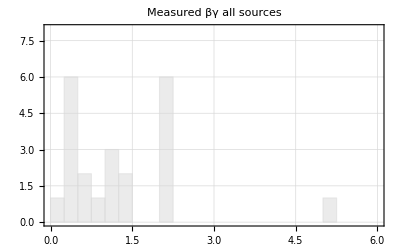

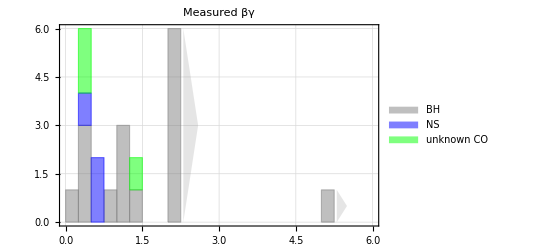

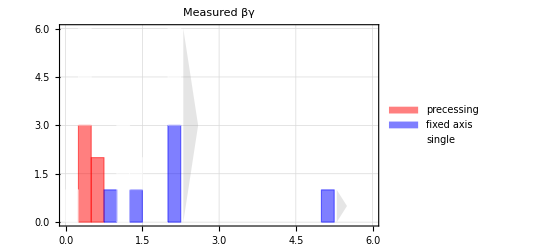

```mathematica
(* plot intrinsic speeds *)


t1=Graphics[{Opacity[0.2],Gray,Triangle[{{3.25,5},{3.25,0},{4,2.5}}]}];
t1a=Graphics[{Opacity[0.2],Gray,Triangle[{{5.775,1},{5.75,0},{6.25,0.5}}]}];
t2=Graphics[{Opacity[0.2],Gray,Triangle[{{3.25,5},{3.25,0},{4.05,2.5}}]}];
t2a=Graphics[{Opacity[0.2],Gray,Triangle[{{5.5,1},{5.5,0},{6.3,0.5}}]}];
t3=Graphics[{Opacity[0.2],Gray,Triangle[{{3.25,4},{3.25,0},{3.5,2}}]}];
t3a=Graphics[{Opacity[0.2],Gray,Triangle[{{5.75,1},{5.75,0},{6,0.5}}]}];
t4=Graphics[{Opacity[0.2],Gray,Triangle[{{2.3,6},{2.3,0},{2.59,3}}]}];
t4a=Graphics[{Opacity[0.2],Gray,Triangle[{{5.3,1},{5.3,0},{5.5,0.5}}]}];
(* The 'alljets' plots *)

realbetas=Histogram[{alljets[[All,6]]},{0.05},ChartStyle->{LightGray},PlotRange->{{0.0,1.1},{0,8}},PlotLabel->"Fractional speed of light β",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

Show[realbetas];
Export["physics1a.pdf",%];

realgammas=Histogram[{alljets[[All,7]]},{0.25},ChartStyle->{LightGray},PlotRange->{{1.0,6},{0,10}},PlotLabel->"Lorentz factor γ",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

Show[realgammas,t1,t1a];
Export["physics1b.pdf",%];

realbetagammas=Histogram[{alljets[[All,8]]},{0.25},ChartStyle->{LightGray},PlotRange->{{0.0,6},{0,8}},PlotLabel->"Measured βγ all sources",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"]

Show[realbetagammas,t2,t2a];
Export["physics1c.pdf",%];

(* The 'source types without URFs' plots *)

realbetassepnourf=Histogram[{bh[[All,6]],nsnourf[[All,6]],unknourf[[All,8]]},{0.05},ChartStyle->{Gray,Blue, Green},PlotRange->{{0.0,1.1},{0,6}},ChartLegends->Placed[{"BH","NS","BH/NS?"},{0.7,0.7}],PlotLabel->"Fractional speed of light β (no URF)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

Show[realbetassepnourf];
Export["physics3a.pdf",%];

realgammassepnourf=Histogram[{bh[[All,7]],nsnourf[[All,7]],unknourf[[All,8]]},{0.25},ChartStyle->{Gray,Blue, Green},PlotRange->{{1.0,6},{0,7}},ChartLegends->Placed[{"BH","NS","BH/NS?"},{0.7,0.7}],PlotLabel->"Lorentz factor γ (no URF)",PlotTheme->{"Detailed","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

Show[realgammassepnourf,t3,t3a];
Export["physics3b.pdf",%];

realbetagammassepnourf=Histogram[{bh[[All,8]],nsnourf[[All,8]],unknourf[[All,8]]},{0.25},ChartStyle->{Gray,Blue, Green},PlotRange->{{0.0,6},{0,6}},ChartLegends->Placed[{"BH","NS","unknown CO"},{0.7,0.7}],PlotLabel->"Measured βγ ",PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

sf1=Show[realbetagammassepnourf,t4,t4a]
Export["physics3c.pdf",sf1];
Export["physics3c.png",sf1];
Export["SCIENCEFIG1.pdf",sf1];
Export["SCIENCEFIG1.png",sf1];

(* PRECESSION or not *)

realprecnonprec=Histogram[{prec[[All,8]],nonprecnourf[[All,8]]},{0.25},PlotRange->{{0.0,16},{0,6}},ChartLegends->Placed[{"precessing","no precession"},{0.8,0.8}],PlotLabel->"βγ",PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

Show[realprecnonprec,t2];
Export["physics4a.pdf",%];

realprecnonprecnourf=Histogram[{prec[[All,8]],nonprecnourf[[All,8]]},{0.25},PlotRange->{{0.0,6},{0,6}},ChartLegends->Placed[{"precessing","fixed axis"},{0.8,0.8}],PlotLabel->"Measured βγ",PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

sf2=Show[realprecnonprecnourf,t4,t4a];
Export["physics4b.pdf",sf2];
Export["physics4b.png",sf2];

realprecnonprecnourf3way=Histogram[{prec[[All,8]],fixednourf[[All,8]],singlenourf[[All,8]]},{0.25},ChartStyle->{Red,Blue, White},PlotRange->{{0.0,6},{0,6}},ChartLegends->Placed[{"precessing","fixed axis","single"},{0.8,0.8}],PlotLabel->"Measured βγ",PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"},ChartLayout->"Stacked"];

sf3=Show[realprecnonprecnourf3way,t4,t4a]
Export["prec3way.pdf",sf3];
Export["prec3way.png",sf3];
Export["SCIENCEFIG2.pdf",sf3];
Export["SCIENCEFIG2.png",sf3];
```

```mathematica
(* K-S and A-D tests *)

(* remember columns! 2 are proper motions, 4 are apparent speeds, 6 is real beta, 7 real gamma, 8 real beta*gamma *)

Print["All BH vs NS actual speeds with no URFs"];

K=KolmogorovSmirnovTest[bh[[All,8]],nsnourf[[All,8]],"HypothesisTestData"];
K["TestDataTable"]//TraditionalForm
K["TestConclusion"]//TraditionalForm

K2=AndersonDarlingTest[bh[[All,8]],nsnourf[[All,8]],"HypothesisTestData"];
K2["TestDataTable"]//TraditionalForm
K2["TestConclusion"]//TraditionalForm
```

All BH vs NS actual speeds with no URFs

| Statistic | P-Value
Kolmogorov-Smirnov | 0.75 | 0.0722394

The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

| Statistic | P-Value
Anderson-Darling | 2.35066 | 0.0597946

The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Anderson-Darling test.

```mathematica
Print["Slow BH vs NS actual speeds with no URFs"];

K=KolmogorovSmirnovTest[slowbh[[All,8]],nsnourf[[All,8]],"HypothesisTestData"];
K["TestDataTable"]//TraditionalForm
K["TestConclusion"]//TraditionalForm

K2=AndersonDarlingTest[slowbh[[All,8]],nsnourf[[All,8]],"HypothesisTestData"];
K2["TestDataTable"]//TraditionalForm
K2["TestConclusion"]//TraditionalForm
```

Slow BH vs NS actual speeds with no URFs

| Statistic | P-Value
Kolmogorov-Smirnov | 0.466667 | 0.678571

The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

| Statistic | P-Value
Anderson-Darling | 0.83841 | 0.448789

The null hypothesis that the datasets have the same distribution is not rejected at the 5 percent level based on the Anderson-Darling test.

```mathematica
Print["Precessing vs definitely fixed axis actual speeds with no URFs"]

M=KolmogorovSmirnovTest[prec[[All,8]],fixednourf[[All,8]],"HypothesisTestData"];
M["TestDataTable"]//TraditionalForm
M["TestConclusion"]//TraditionalForm
(* Precessing vs non-precessing differ at 99% confidence *)

M2=AndersonDarlingTest[prec[[All,8]],fixednourf[[All,8]],"HypothesisTestData"];
Print["Precessing vs definitely fixed apparent speeds with no URFs"]
M2["TestDataTable"]//TraditionalForm
M2["TestConclusion"]//TraditionalForm
(* Precessing vs non-precessing differ at 99% confidence *)
```

Precessing vs definitely fixed axis actual speeds with no URFs

| Statistic | P-Value
Kolmogorov-Smirnov | 1 | 0.004329

The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

Precessing vs definitely fixed apparent speeds with no URFs

| Statistic | P-Value
Anderson-Darling | 5.39389 | 0.00201399

The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Anderson-Darling test.

```mathematica
(* comparison to spins *)
```

{{4U1543,187,5.,5.40462,10,0.982,5.3,5.2,BH,>F,L,0.98,0.8,0},{XTEJ1550,65,4.4,1.65318,70,0.9,2.29416,2.06474,BH,>F,?,0.55,0.34,0.34},{MAXIJJ1820(fast),77,3.,1.33526,70,0.9,2.29416,2.06474,BH,>F,?,0.988,0.14,0.8},{GRS1915,24,9.4,1.30405,65,0.894763,2.23943,2.00376,BH,>F,L,0.98,0.95,0.71},{GROJ1655,54,3.2,0.998844,85,0.9,2.29416,2.06474,BH,>F,L?,0.98,0.7,0.29}}

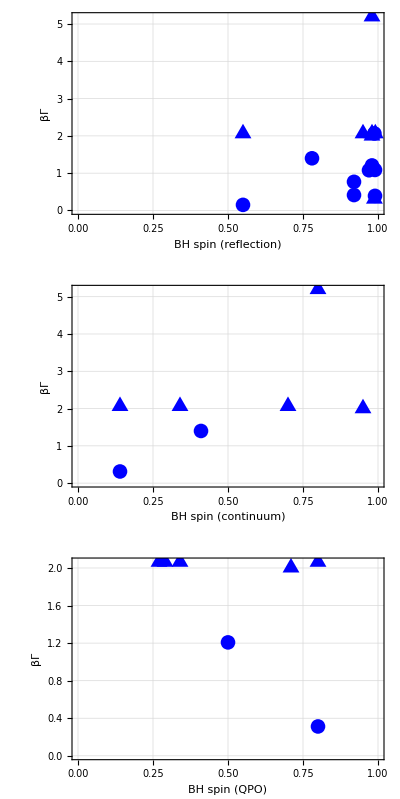

```mathematica
(* Reflection spins first *)


reflections={ j1348, j1535,h1743, j1848, j1752, exo1846, v404, x1908,j1820f};
reflectionslimits={u1543, gx339,j1550,j1820s,j1803,grs1915,groj1655};

(* need to make separate subset for which speeds are limits and which are not for each spin type *)
(* and can then use the "▲" graphic ("\FilledUpTriangle" with [ ]around the name]) *)

(* the sources with speed lower limits are 1543, 339, 1550, 1803, 1820, 1655 and 1915 *)

continuums={ j1348,j1820s};
continuumslimits={u1543,j1550, j1820f, grs1915,groj1655}

qpos={h1743,j1820s};
qposlimits={gx339,j1550,j1820f,grs1915,groj1655};

rr=Thread[{reflections[[All,12]],reflections[[All,8]]}];
rrl=Thread[{reflectionslimits[[All,12]],reflectionslimits[[All,8]]}];

cc=Thread[{continuums[[All,13]],continuums[[All,8]]}];
ccl=Thread[{continuumslimits[[All,13]],continuumslimits[[All,8]]}];

qq=Thread[{qpos[[All,14]],qpos[[All,8]]}];
qql=Thread[{qposlimits[[All,14]],qposlimits[[All,8]]}];

rrp=ListPlot[{rr,rrl},PlotRange->{{0,1},All},FrameLabel->{"BH spin (reflection)","βΓ"},PlotStyle -> {Blue,Blue},PlotMarkers->{{"●",Offset[15]},{"▲",Offset[20]}},PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"}];

ccp=ListPlot[{cc,ccl},PlotRange->{{0,1},All},FrameLabel->{"BH spin (continuum)","βΓ"},PlotStyle -> {Blue,Blue},PlotMarkers->{{"●",Offset[15]},{"▲",Offset[20]}},PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"}];

qqp=ListPlot[{qq,qql},PlotRange->{{0,1},All},FrameLabel->{"BH spin (QPO)","βΓ"},PlotStyle -> {Blue,Blue},PlotMarkers->{{"●",Offset[15]},{"▲",Offset[20]}},PlotTheme->{"Scientific","PlotMarkers","LargeLabels","Grid"}];

spintests=GraphicsColumn[{rrp,ccp,qqp}]
Export["spintests.pdf",spintests];
Export["spintests.png",spintests];
Export["SCIENCEFIG3.pdf",spintests];
Export["CIENCEFIG3.png",spintests];
```

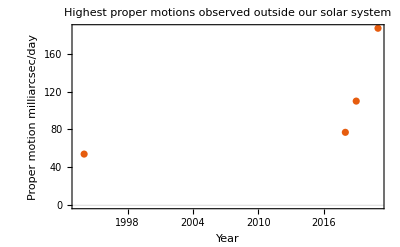

srp.png

```mathematica
(* Plot evolution of galactic proper motion speed record since 1995... *)

speedrecords={{1994,54},{2018,77},{2019,110},{2021,187}};
srp=ListPlot[{speedrecords},PlotTheme->"Scientific",PlotLabel->"Highest proper motions observed outside our solar system",FrameLabel->{"Year","Proper motion milliarcsec/day"}]
Export["srp.png",srp]
```

```mathematica
speedrecords
```

{{1994,54},{2018,77},{2019,110},{2021,187}}